```mathematica
c[{i_,j_}]:={White,Disk[{2j+i,-i},1],Black,Circle[{2j+i,-i},1]}
```

```mathematica
c[{i_,j_},cc_]:={col[[cc]],Disk[{2j+i,-i},1],Black,Circle[{2j+i,-i},1]}
```

```mathematica
col={Hue[0,.2],Hue[.17,.2],Hue[.35,.2],Hue[.6,.2],Hue[.1,.2],Hue[.8,.2]};
```

```mathematica
before[L_]:=Graphics[Map[If[Position[L,#]=={},c[#],c[#,Position[L,#][[1,1]]]]&,Flatten[Table[{i,j},{i,1,n},{j,1,n+1-i}],1]],ImageSize->30(n+1),PlotRange->{{1,2n+3},{-n-3/2,1/2}}]
```

```mathematica
after[L_]:=Graphics[{Map[If[Position[L,#]=={},c[#],c[#,Position[L,#][[1,1]]]]&,Flatten[Table[{i,j},{i,1,n},{j,1,n+1-i}],1]],MapIndexed[Text[#1,{#2[[1]]+2#2[[2]],-#2[[1]]}]&,sel[L][[1]],{2}]},ImageSize->30(n+1),PlotRange->{{1,2n+3},{-n-3/2,1/2}}]
```

```mathematica
tot[L_]:=Module[{to,t},
to={L};t=L;
While[Length[t]>1,
t=Map[Total,Partition[t,2,1]];
AppendTo[to,t]];to]
```

```mathematica
dup[L_]:=Module[{},
f=Flatten[L];
p=Union[Select[Map[Position[L,#]&,f],Length[#]>1&]]]
```

```mathematica
sel[L_]:=Select[poss,dup[#]==L&]
```

```mathematica
g[nn_]:=Module[{},
n=nn;
poss=Select[Map[tot[Rest[IntegerDigits[#]]]&,Range[10^n,2*10^n-1]],Not[MemberQ[Flatten[#],0]]&];
d=Map[dup,poss];
dd=Union[d];
ddd=Table[Length[Select[d,#==dd[[i]]&]],{i,1,Length[dd]}];
s=Flatten[Position[ddd,1],1];
ss=Map[dd[[#]]&,s];
ss=Select[ss,Union[Map[Length,#]]=={2}&];
For[k=1,k≤Length[ss],k++,
Print[before[ss[[k]]]];Print[after[ss[[k]]]]]]
```

-Graphics-

```mathematica
g[3]
```

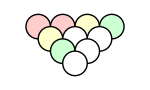

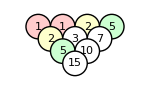

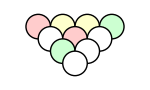

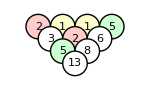

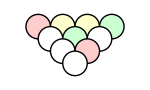

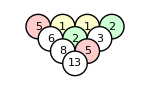

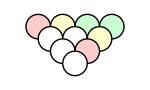

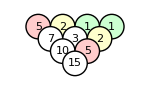

```mathematica
g[4]
```

```mathematica
For[k=1,k≤Length[ss],k++,
Print[before[ss[[k]]]];Print[after[ss[[k]]]]]
```

## 5x5 2 colors

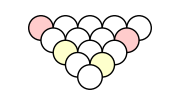

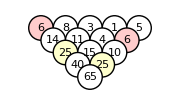

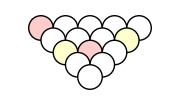

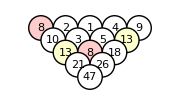

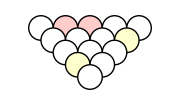

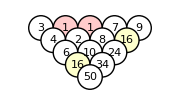

## 5x5 3 colors

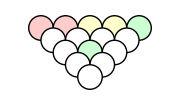

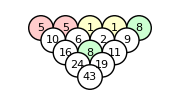

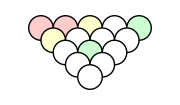

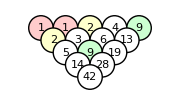

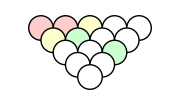

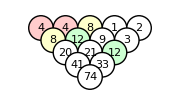

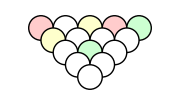

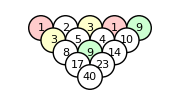

## 5x5 4+ colors

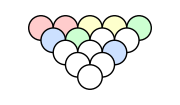

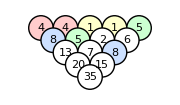

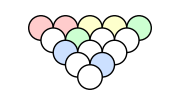

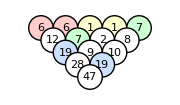

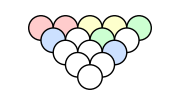

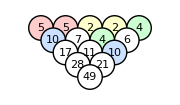

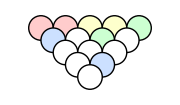

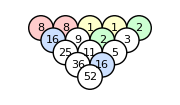

-Graphics-

-Graphics-

-Graphics-

«283 more identical outputs»

## 6x6 triangle

```mathematica
n=6;poss={};
For[a1=1,a1≤9,a1++,
For[a2=1,a2≤9,a2++,
For[a3=1,a3≤9,a3++,
For[a4=1,a4≤9,a4++,
For[a5=1,a5≤9,a5++,
For[a6=1,a6≤9,a6++,
temp=tot[{a1,a2,a3,a4,a5,a6}];
q=dup[temp];
If[Union[Map[Length,q]]=={2}&&Length[q]≤6,AppendTo[poss,temp]]]]]]]];
d=Map[dup,poss];
dd=Union[d];
ddd=Table[Length[Select[d,#==dd[[i]]&]],{i,1,Length[dd]}];
s=Flatten[Position[ddd,1],1];
ss=Map[dd[[#]]&,s];
For[k=1,k≤Length[ss],k++,
Print[before[ss[[k]]]];Print[after[ss[[k]]]]]
```

-Graphics-

-Graphics-

-Graphics-

«1537 more identical outputs»